```mathematica
averageListCorrelation[listOfLists_]:=Module[{correlations},
correlations=Flatten[Outer[Correlation,listOfLists,listOfLists,1]];
N[Mean[correlations]]];

Correlations[listOfLists_]:=Flatten[Outer[Correlation,listOfLists,listOfLists,1]]
```

```mathematica
rotateListsForMaxAverageCorrelation[listOfLists_]:=Module[{rotatedLists,maxAvgCorrelation,currentAvgCorrelation,maxCorrelationOrders},
rotatedLists=listOfLists;
maxAvgCorrelation=-Infinity;
maxCorrelationOrders = listOfLists;
Do[
Print[i];
Do[
currentAvgCorrelation=averageListCorrelation[rotatedLists];

If[currentAvgCorrelation>maxAvgCorrelation,
maxAvgCorrelation=currentAvgCorrelation;
maxCorrelationOrders = rotatedLists;
(*Uncomment the next line to see intermediate results*)Print["List ",i," Iteration ",j,": Max Average Correlation = ",maxAvgCorrelation];];


rotatedLists[[i]]=RotateLeft[rotatedLists[[i]]];
,{j,Length[rotatedLists[[i]]]}]

,{i,Length[listOfLists]}];
{maxAvgCorrelation,maxCorrelationOrders}]
```

```mathematica
Statistical = Import["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Volume_2048_statistical.csv"];
```

```mathematica
sorted[[1,2]]
```

6511.41

```mathematica
sorted = SortBy[Statistical,-#[[2]]&];
MegaList = Table[ToExpression@ StringSplit[sorted[[i,1]],":"],{i,100}];
```

```mathematica
res=rotateListsForMaxAverageCorrelation[MegaList];
```

1

List 1 Iteration 1: Max Average Correlation = 0.0517139

List 1 Iteration 7: Max Average Correlation = 0.053463

2

3

4

5

6

List 6 Iteration 20: Max Average Correlation = 0.0535333

7

8

9

10

11

12

13

14

List 14 Iteration 20: Max Average Correlation = 0.05368

15

16

17

18

19

20

21

22

23

24

List 24 Iteration 29: Max Average Correlation = 0.054446

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

```mathematica
Do[
res = rotateListsForMaxAverageCorrelation[res[[2]]];
,{i,10}]
```

1

List 1 Iteration 1: Max Average Correlation = 0.154048

List 1 Iteration 7: Max Average Correlation = 0.170167

List 1 Iteration 15: Max Average Correlation = 0.170586

List 1 Iteration 31: Max Average Correlation = 0.173754

2

List 2 Iteration 3: Max Average Correlation = 0.177349

List 2 Iteration 5: Max Average Correlation = 0.200078

3

4

5

6

List 6 Iteration 12: Max Average Correlation = 0.200825

7

8

9

10

1

List 1 Iteration 1: Max Average Correlation = 0.200825

List 1 Iteration 7: Max Average Correlation = 0.22043

List 1 Iteration 15: Max Average Correlation = 0.221268

List 1 Iteration 31: Max Average Correlation = 0.235044

2

List 2 Iteration 5: Max Average Correlation = 0.257538

3

4

5

6

7

8

9

10

1

List 1 Iteration 1: Max Average Correlation = 0.257538

List 1 Iteration 7: Max Average Correlation = 0.258176

List 1 Iteration 15: Max Average Correlation = 0.270891

List 1 Iteration 31: Max Average Correlation = 0.28944

2

3

4

List 4 Iteration 11: Max Average Correlation = 0.292319

List 4 Iteration 27: Max Average Correlation = 0.295481

List 4 Iteration 32: Max Average Correlation = 0.30511

5

6

7

8

9

10

1

List 1 Iteration 1: Max Average Correlation = 0.30511

List 1 Iteration 15: Max Average Correlation = 0.313116

List 1 Iteration 31: Max Average Correlation = 0.338507

2

3

4

5

6

7

8

List 8 Iteration 11: Max Average Correlation = 0.340654

List 8 Iteration 16: Max Average Correlation = 0.356982

9

10

1

List 1 Iteration 1: Max Average Correlation = 0.356982

List 1 Iteration 15: Max Average Correlation = 0.366789

List 1 Iteration 31: Max Average Correlation = 0.398072

2

3

4

5

6

7

8

9

10

List 10 Iteration 6: Max Average Correlation = 0.418378

1

List 1 Iteration 1: Max Average Correlation = 0.418378

List 1 Iteration 15: Max Average Correlation = 0.430414

List 1 Iteration 31: Max Average Correlation = 0.466732

2

3

4

5

6

7

8

9

10

1

List 1 Iteration 1: Max Average Correlation = 0.466732

2

3

List 3 Iteration 15: Max Average Correlation = 0.520274

4

5

6

7

8

9

10

1

List 1 Iteration 1: Max Average Correlation = 0.520274

2

3

4

5

6

7

List 7 Iteration 3: Max Average Correlation = 0.524067

List 7 Iteration 6: Max Average Correlation = 0.557018

List 7 Iteration 15: Max Average Correlation = 0.584343

8

9

10

1

List 1 Iteration 1: Max Average Correlation = 0.584343

2

3

4

5

6

7

8

9

10

1

List 1 Iteration 1: Max Average Correlation = 0.584343

2

3

4

5

6

7

8

9

10

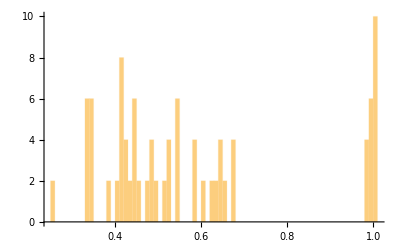

```mathematica
Histogram[N[Correlations[res[[2]]]],100]
```

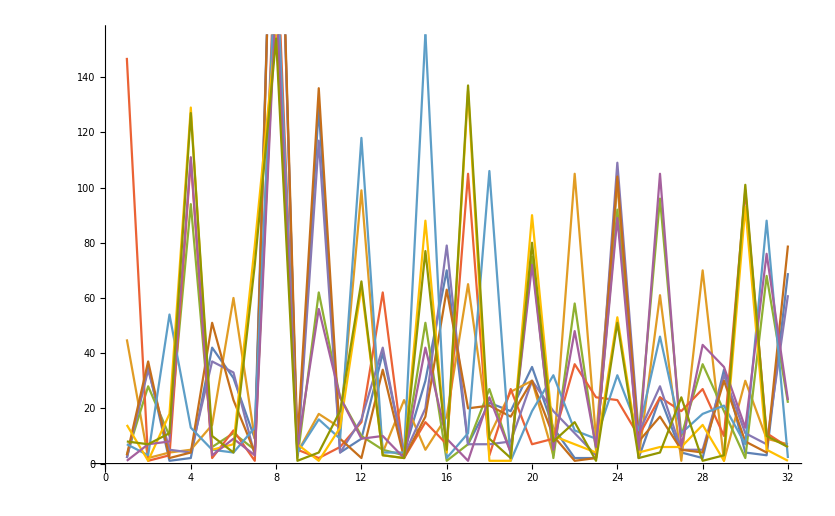

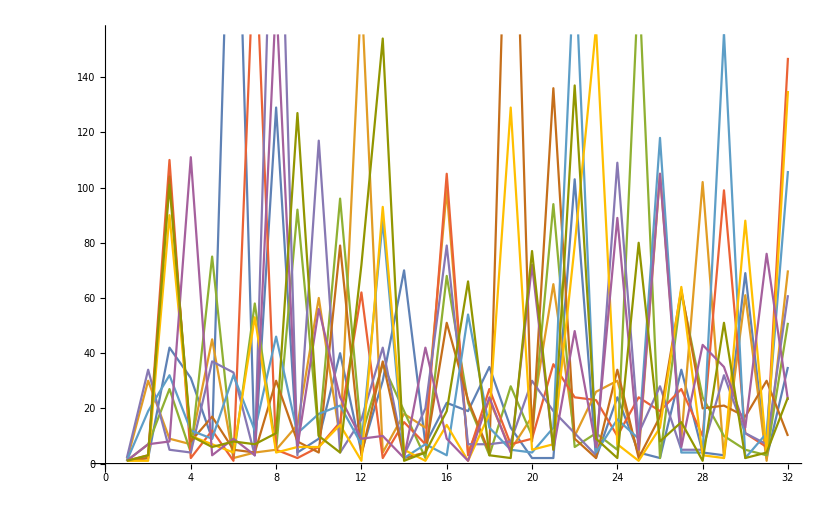

```mathematica
ListLinePlot[res[[2]]]
ListLinePlot[MegaList]
```

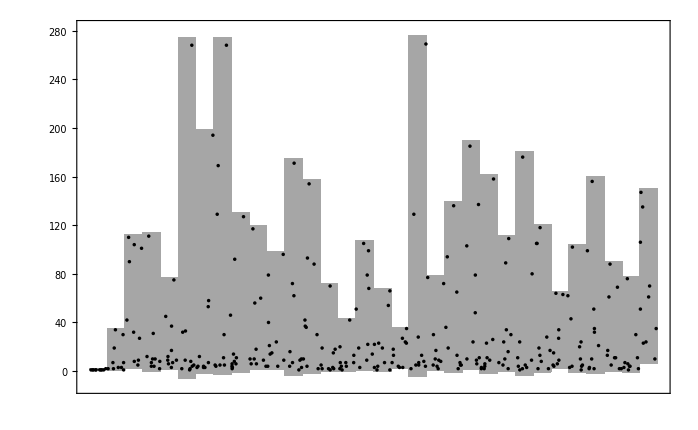

```mathematica
DistributionChart[Transpose[MegaList],ChartElementFunction->ChartElementData["PointDensity"],ChartStyle-> {Directive[EdgeForm[None],Orange]},BarSpacing->0]
```

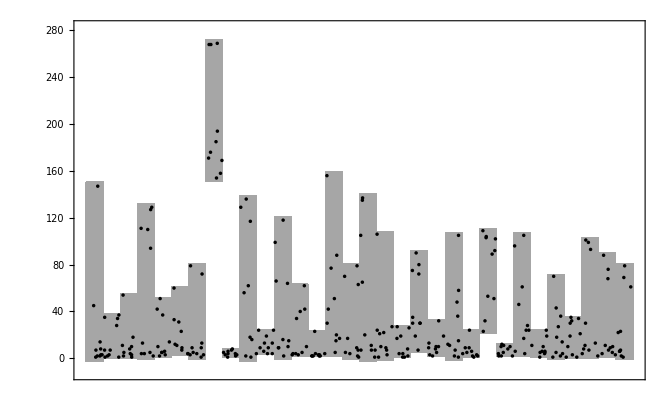

```mathematica
DistributionChart[Transpose[res[[2]]],ChartElementFunction->ChartElementData["PointDensity"],ChartStyle-> {Directive[EdgeForm[None],Orange]},BarSpacing->0]
```

```mathematica
DistributionChart[Transpose[MegaList],ChartElementFunction->ChartElementData["Density"],ChartStyle-> {Directive[EdgeForm[None],Orange]},BarSpacing->0]
```

-Graphics-

```mathematica
{1,2,3}-{1,2,1}
```

{0,0,2}

```mathematica
listOfLists = {{0,1,2},{2,1,4},{1,.99,1}};
Flatten[Outer[Distance,listOfLists,listOfLists,1]]
```

{0,2 √2,1.41425,2 √2,0,3.16229,1.41425,3.16229,0.}

```mathematica
Distance[{1,2,3},{2,2,2}]
```

√2